Evyn Marsh

```mathematica
Integrate[ArcTan[x]/(x^2), x]
```

-ArcTan[x]/x+Log[x]-1/2 Log[1+x^2]

```mathematica
Integrate[(x^8)E^x, x]
```

ⅇ^x (40320-40320 x+20160 x^2-6720 x^3+1680 x^4-336 x^5+56 x^6-8 x^7+x^8)

```mathematica
Integrate[((x^4) + (5x^2) - 7x)/ ((x^2 - 4x +4)((x^2) + 3) (x - 1)), x]
```

1/392 (-1232/(-2+x)-114 √3 ArcTan[x/(√3)]-98 Log[1-x]+584 Log[2-x]-47 Log[3+x^2])

```mathematica
NItegrate[E^(x^2), {x,2,5}]
```

NItegrate[ⅇ^(x^2),{x,2,5}]

```mathematica
N[%]
```

NItegrate[2.71828^(x^2),{x,2.,5.}]

```mathematica
NIntegrate[E^(x^2), {x,2,5}]
```

7.35415×10^9

```mathematica
NIntegrate[x*Cos[Sqrt[x]], {x,Pi/6, Pi/3}]
```

0.255172

```mathematica
NIntegrate[Sqrt[1 + 16x^5], {x, 7, 10}]
```

2576.9

```mathematica
f[x_]= x^2 + Sqrt[x + 2] + Log[x^2 + 7] + E^x - Sin[x^7]
```

ⅇ^x+x^2+√(2+x)+Log[7+x^2]-Sin[x^7]

```mathematica
q = f'[x]
```

ⅇ^x+2 x+1/(2 √(2+x))+(2 x)/(7+x^2)-7 x^6 Cos[x^7]

```mathematica
NIntegrate[Sqrt[1 +q^2], {x, 3,7}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.53119}. NIntegrate obtained 508967. and 22393.5 for the integral and error estimates.

508967.

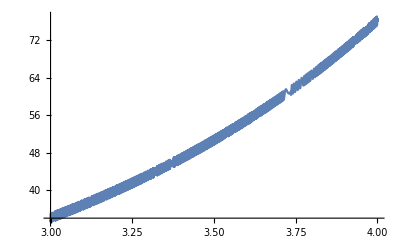

```mathematica
Plot[f[x], {x,3,4}]
```

```mathematica
NIntegrate[Sqrt[1 +q^2], {x, 3,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.85544}. NIntegrate obtained 49174.7 and 2306.65 for the integral and error estimates.

49174.7

```mathematica
NIntegrate[Sqrt[1 +q^2], {x, 5,7}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.94261690752226}. NIntegrate obtained 466892. and 22763. for the integral and error estimates.

466892.

```mathematica
49174.7 + 466892
```

```mathematica
516066.7 No
```

```mathematica
f[x_] = Sqrt[100- ((100x^2)/36)]
```

√(100-(25 x^2)/9)

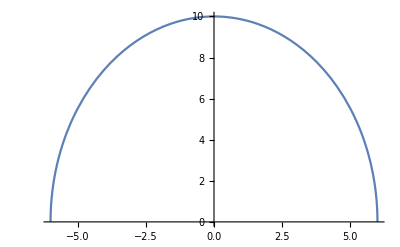

```mathematica
Plot[f[x],{x,-6,6}]
```

```mathematica
NIntegrate[Sqrt[1+(f'[x])^2], {x,-6,6}]
```

25.527

```mathematica
N[%] * 2
```

51.054

```mathematica
NIntegrate[6x^4 +y^2 + x*y +3, {x,-2,3},{y,0,2}]
```

708.333

```mathematica
Clear y,x
```

```mathematica
y= x^2
```

x^2

```mathematica
q= Log[x+1]
```

Log[1+x]

```mathematica
FindRoot[y-q,{x,-.5,.5}]
```

{x→-4.23085×10^-17}

```mathematica
FindRoot[y-q,{x,.5,1}]
```

{x→0.746882}

```mathematica
NIntegrate[Pi *(((Log[x+1])^2)-(x^2)^2), {x,0,.746882}]
```

0.131746

```mathematica
Clear y,x,y[x]
Clear x, y
```

```mathematica
Clear y
```

Clear x^2

```mathematica
Clear[y,x]
```

```mathematica
DSolve[y''[x]-y'[x]==0,y[x],x]
```

{{y[x]→ⅇ^x C[1]+C[2]}}

```mathematica
Clear[y,x]
```

```mathematica
DSolve[{y''[x]-y'[x]==0,y[0]==0,y[1]==1},y[x],x]
```

{{y[x]→(-1+ⅇ^x)/(-1+ⅇ)}}

```mathematica
Clear[y,x]
```

```mathematica
DSolve[y'''[x]-6y''[x]+11y'[x]-6y[x]==0,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(3 x) C[3]}}

```mathematica
Clear[y,x]
```

```mathematica
DSolve[y'''[x]-6y''[x]+11y'[x]-6y[x]==3x,y[x],x]
```

{{y[x]→1/12 (-11-6 x)+ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(3 x) C[3]}}

```mathematica
Clear[y,x]
```

```mathematica
DSolve[{y'''[x]-6y''[x]+11y'[x]-6y[x]==3x,y[2]==1,y'[3]==3,y''[1]==6},y[x],x]
```

{{y[x]→-((-99 ⅇ^6+242 ⅇ^7-154 ⅇ^9+33 ⅇ^10+168 ⅇ^(3 x)+378 ⅇ^(3+x)-168 ⅇ^(4+x)-630 ⅇ^(5+x)+420 ⅇ^(7+x)+144 ⅇ^(8+x)-216 ⅇ^(9+x)-378 ⅇ^(1+2 x)+315 ⅇ^(2+2 x)+42 ⅇ^(3+2 x)-72 ⅇ^(5+2 x)-105 ⅇ^(6+2 x)+216 ⅇ^(7+2 x)-182 ⅇ^(1+3 x)+142 ⅇ^(3+3 x)-144 ⅇ^(4+3 x)-54 ⅇ^6 x+132 ⅇ^7 x-84 ⅇ^9 x+18 ⅇ^10 x)/(12 ⅇ^6 (-9+22 ⅇ-14 ⅇ^3+3 ⅇ^4)))}}